```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 320 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,VariationalMethods`,System`,Global`}

```mathematica
Clear[s]
s = { r[t] Cos[θ[t]] , r[t] Sin[θ[t]] }
```

{Cos[θ[t]] r[t],r[t] Sin[θ[t]]}

```mathematica
D[s, t]
```

{Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t],Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t]}

```mathematica
D[s, t] . D[s, t]
```

(Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t])^2+(Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t])^2

```mathematica
D[s, t] . D[s, t]  // Expand
```

Cos[θ[t]]^2 r'[t]^2+Sin[θ[t]]^2 r'[t]^2+Cos[θ[t]]^2 r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[s, t] . D[s, t]  // Expand  // Simplify
```

r'[t]^2+r[t]^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 m1 ( D[s, t] . D[s, t]  // Expand  // Simplify  ) + 1/2 m2 r'[t]^2
```

1/2 m2 r'[t]^2+1/2 m1 (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
Clear[V] 
V =- m2 g ( l -r[t] )
```

-g m2 (l-r[t])

```mathematica
Clear[ℒ]
ℒ  = T - V
```

g m2 (l-r[t])+1/2 m2 r'[t]^2+1/2 m1 (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
ℒ // pdConv
```

g m2 (l-r(t))+1/2 m1 ((r(t))^2 ((∂θ(t))/(∂t))^2+((∂r(t))/(∂t))^2)+1/2 m2 ((∂r(t))/(∂t))^2

```mathematica
Clear[q]
q = { r[t] , θ[t] }
```

{r[t],θ[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ]
```

g m2-m1 r[t] θ'[t]^2+m1 r''[t]+m2 r''[t]

2 m1 r[t] r'[t] θ'[t]+m1 r[t]^2 θ''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ] , t ] - D[ ℒ , q[[i]] ] == 0 ,
{i,1,2 } ] // TableForm
```

g m2-m1 r[t] θ'[t]^2+m1 r''[t]+m2 r''[t]==0
2 m1 r[t] r'[t] θ'[t]+m1 r[t]^2 θ''[t]==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-g m2+m1 r[t] θ'[t]^2-(m1+m2) r''[t]==0
-m1 r[t] (2 r'[t] θ'[t]+r[t] θ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
m1 -> 20 ,
m2 -> 5 ,
g -> 9.8 
} ;
parameters // TableForm
```

m1→20
m2→5
g→9.8

```mathematica
eqs /. parameters // TableForm
```

-49.+20 r[t] θ'[t]^2-25 r''[t]==0
-20 r[t] (2 r'[t] θ'[t]+r[t] θ''[t])==0

```mathematica
Clear[ics]
ics = {
r[0] == 2 ,
r'[0] == 1 , 
θ[0] == 0 ,
θ'[0] == 12 
} ;
ics // TableForm
```

r[0]==2
r'[0]==1
θ[0]==0
θ'[0]==12

```mathematica
Clear[solution]
solution = 
NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 50 } ]
```

{{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}}

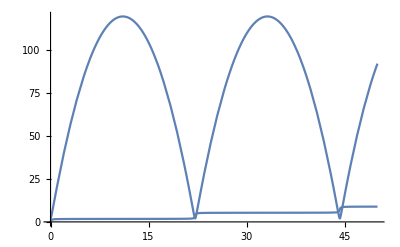

```mathematica
Plot[ q /. solution , { t, 0, 50 } ]
```

```mathematica
Exit[]
Quit[]
```